# Coupled Exponentials & Logarithms

©  Copyright 2020 Kenric Nelson

   Licensed under the Apache License, Version 2.0 (the “License”);
you may not use this file except in compliance with the License.
You may obtain a copy of the License at

    http://www.apache.org/licenses/LICENSE-2.0

Unless required by applicable law or agreed to in writing, software
distributed under the License is distributed on an “AS IS” BASIS,
WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
See the License for the specific language governing permissions and
limitations under the License.

## Graphic of Coupled Exponential

Graph shows curves from linear (κ = -0.5) to exponential (κ = 0)

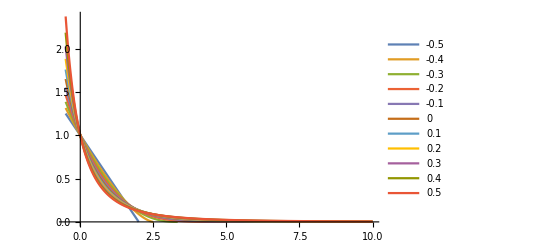

```mathematica
CouplingValues = {-0.5,-0.4,-0.3,-0.2,-0.1,0, 0.1,0.2,0.3,0.4,0.5};
Plot[CoupledExponential[x,#]^-1&/@CouplingValues//Evaluate,{x,-0.5,10},PlotLegends->CouplingValues,PlotRange->Full]
```

The curves are produced by the Coupled Exponential Function
	(1+κ x)^(-(1 + κ)/κ)

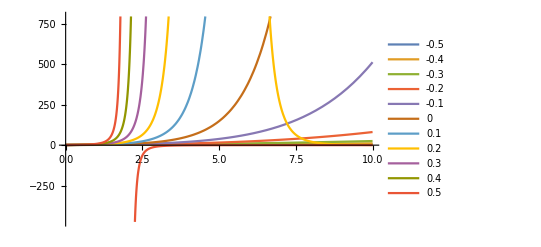

```mathematica
CouplingValues = {-0.5,-0.4,-0.3,-0.2,-0.1,0, 0.1,0.2,0.3,0.4,0.5};
Plot[CoupledExponential[-x,#]^-1&/@CouplingValues//Evaluate,{x,0,10},PlotLegends->CouplingValues]
```

The curves are produced by the Coupled Exponential Function
	(1-κ x)^((1 + κ)/-κ)

## Graphic of Coupled Logarithm

Graph shows curves from linear to logarithmic

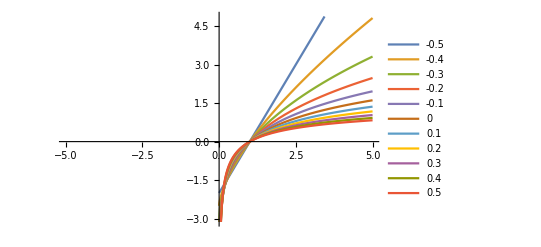

```mathematica
CouplingValues = {-0.5,-0.4,-0.3,-0.2,-0.1,0, 0.1,0.2,0.3,0.4,0.5};
Quiet[Plot[
-CoupledLogarithm[x^-1,#]&/@CouplingValues//Evaluate,{x,-5,5},
PlotLegends->CouplingValues],
{Power::infy}]
```

The curves are produced by the Coupled Logarithmic Function
	1/(- κ)(x^((- κ)/(1+ κ))-1)

## Coupled Normal Distribution

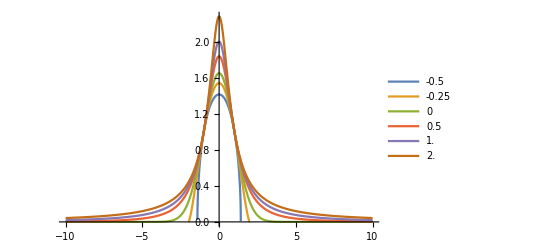

```mathematica
CouplingValues = {-0.5,-0.25,0,0.5,1.0,2.0};
Quiet[Plot[
PDF[CoupledNormalDistribution[0,1,#],{x}]/PDF[CoupledNormalDistribution[0,1,#],{1}]&/@CouplingValues//Evaluate,{x,-10,10},
PlotLegends->CouplingValues,
PlotRange->Full],
{Power::infy}]
```

## Coupled Gaussian is Scale-Free as σ → 0

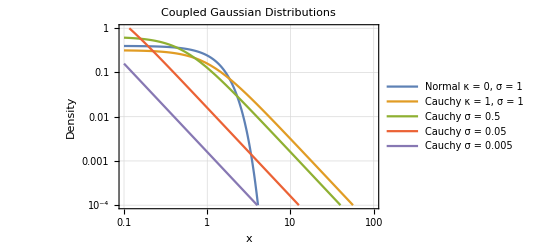

```mathematica
Parameters={{1,1,0.5,0.05,0.005},{0,1,1,1,1}};
Quiet[LogLogPlot[MapThread[
PDF[CoupledNormalDistribution[0,#1,#2],{x}]&,Parameters]//Evaluate,{x,0.1,100},
PlotLegends->{"Normal κ = 0, σ = 1", "Cauchy κ = 1, σ = 1","Cauchy σ = 0.5",
"Cauchy σ = 0.05","Cauchy σ = 0.005"},
LabelStyle->Directive[Gray,Smaller],
PlotRange->{{0.1,100},{10^-4,1}},
PlotTheme->{"Detailed"},
FrameLabel->{"x","Density"},
PlotLabel->"Coupled Gaussian Distributions"],
{Power::infy}]
```

## Multivariate Coupled Distribution

### Multivariate Coupled Exponential

```mathematica
Plot3D[PDF[MultivariateCoupledDistribution[{1,2},{{1,0},{0,1}},2,1],
{x,y}],
{x,0,5},{y,0,5},
PlotLegends->None,
PlotTheme->"Detailed",
PlotRange->Full
]
```

-Graphics3D-

### Multivariate Coupled Gaussian

```mathematica
Plot3D[PDF[MultivariateCoupledDistribution[{1,2},{{1,-0.01},{0.01,1}},0.01,2],
{x,y}],
{x,-5,5},{y,-5,5},
PlotLegends->None,
PlotTheme->"Detailed",
PlotRange->Full
]
```

-Graphics3D-